```mathematica
?Circle
?Graphics
?RandomReal
?Plot
?For
?If
```

RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"]}], "]"}] is a two-dimensional graphics primitive that represents a circle of radius StyleBox["r", "TI"] centered at the point StyleBox["x", "TI"], StyleBox["y", "TI"]. 
RowBox[{"Circle", "[", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], "]"}] gives a circle of radius 1. 
RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["θ", "TR"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["2", "TR"]]}], "}"}]}], "]"}] gives a circular arc. 
RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]]}], "}"}]}], "]"}] gives an ellipse with semi-axes of lengths SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]] and SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]], oriented parallel to the coordinate axes.

Graphics[primitives,options] represents a two-dimensional graphical image.

RandomReal[] gives a pseudorandom real number in the range 0 to 1. 
RandomReal[{x_min,x_max}] gives a pseudorandom real number in the range x_min to x_max. 
RandomReal[x_max] gives a pseudorandom real number in the range 0 to x_max.
RandomReal[range,n] gives a list of n pseudorandom reals. 
RandomReal[range,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom reals.

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

For[start,test,incr,body] executes start, then repeatedly evaluates body and incr until test fails to give True.

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

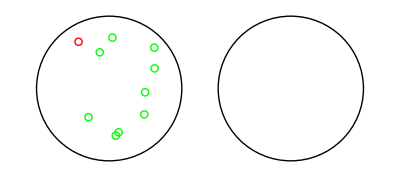

```mathematica
PopC=Table[{k*A,RandomReal[{-Sqrt[2],Sqrt[2]}],RandomReal[{-Sqrt[2],Sqrt[2]}],u},{k,1,10}];
For[j=1,j<1+1,j++,
PopC[[j]][[4]]="i"]

Graphics[
Join[
{{Circle[{0,0},2]},
{Circle[{5,0},2]}},
Table[{
If[
PopC[[i]][[4]]==u,
Green,Red,Red],
Circle[{PopC[[i]][[2]],PopC[[i]][[3]]},.1]},{i,1,Length[PopC]}
]
]
]
```

```mathematica
For[h=1,h<5,h++,
PopC[[h]][[4]]="i"]
```

```mathematica
PopC
```

{{A,-0.843102,1.29162,i},{2 A,0.089434,1.40648,u},{3 A,0.989057,-0.10573,u},{4 A,-0.569055,-0.794579,u},{5 A,0.259295,-1.21145,u},{6 A,0.966444,-0.71691,u},{7 A,0.181745,-1.30294,u},{8 A,1.24909,0.556114,u},{9 A,-0.259115,1.0012,u},{10 A,1.24147,1.13098,u}}

```mathematica
If[PopC[[2]][[4]]=="i",Print["heu"],Print["nope"]]
```

If[u==i,Print[heu],Print[nope]]

```mathematica
2+3
```

5

```mathematica
PopC
```

```mathematica
If[PopC[[2]][[4]]==i , Print["heu"],Print["nope"]]
```

If[u==i,Print[heu],Print[nope]]

```mathematica
PopC[[2]][[4]]==i
```

u==i

```mathematica
u
```

u

```mathematica
Clear[u]
```

```mathematica
If[TrueQ[PopC[[10]][[4]]==u],Print["heu"],Print["nope"]]
```

heu

```mathematica
2+2==4
```

True

```mathematica
u==2
```

u==2

```mathematica
PopC
```

```mathematica
PopC={{A,-0.8431015959660204,1.2916235476721516,"i"},{2 A,0.08943399250289996,1.4064815893156428,"u"},{3 A,0.9890571114444908,-0.10572950362204114,u},{4 A,-0.5690550605547777,-0.7945791862476193,u},{5 A,0.25929548783788015,-1.2114467869019983,u},{6 A,0.9664435857260552,-0.7169097900170232,u},{7 A,0.18174462960585647,-1.3029395435062083,u},{8 A,1.2490941727077907,0.5561140436880336,u},{9 A,-0.2591153049102224,1.0012012287552308,u},{10 A,1.241467781041096,1.1309789150428289,u}}
```

{{A,-0.843102,1.29162,i},{2 A,0.089434,1.40648,u},{3 A,0.989057,-0.10573,u},{4 A,-0.569055,-0.794579,u},{5 A,0.259295,-1.21145,u},{6 A,0.966444,-0.71691,u},{7 A,0.181745,-1.30294,u},{8 A,1.24909,0.556114,u},{9 A,-0.259115,1.0012,u},{10 A,1.24147,1.13098,u}}

```mathematica
?Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

```mathematica
Show[Circle]
```

Show::gtype: Symbol is not a type of graphics.

```mathematica
Show[Circle[]]
```

Show::gtype: Circle is not a type of graphics.

```mathematica
Show[Circle[{0,0}]]
```

Show::gtype: Circle is not a type of graphics.



```mathematica
Show[Graphics[Circle[{0,0}]]]
```



```mathematica
Show[Graphics[Rectangle[]]]
```

```mathematica
?Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u->{u,…},c_v->{v,…},…] links the controls to the specified controllers on an external device.

```mathematica
?Delimiter
```

Delimiter represents a delimiter to be displayed in objects such as PopupMenu and Manipulate.

```mathematica
?Refresh
```

Refresh[expr,opts] represents an object whose value in a Dynamic should be refreshed at times specified by the options opts. 
Refresh[expr,None] specifies that the value of expr should never automatically be refreshed.

```mathematica
Manipulate[
Refresh[
If[moving,
Print"ok ok ok ok ok ok ok ok"
],
UpdateInterval-> If[moving,2,Infinity]
],
{{moving,False,"run simulation"},{True,False}}
]
```